# Majorana-magnon interactions in topological Shiba chains

ABSTRACT (original article): A chain of magnetic impurities deposited on the surface of a superconductor can form a topological Shiba band that supports Majorana zero modes and holds a promise for topological quantum computing. Yet, most experiments scrutinizing these zero modes rely on transport measurements, which only capture local properties. Here we propose to leverage the intrinsic dynamics of the magnetic impurities to access their nonlocal character. We use linear response theory to determine the dynamics of the uniform magnonic mode in the presence of external ac magnetic fields and coupling to Shiba electrons. We demonstrate that this mode, which spreads over the entire chain of atoms, becomes imprinted with the parity of the ground state and, moreover, can discriminate between Majorana and trivial zero modes located at the ends of the chain. Our approach offers a noninvasive alternative to the scanning tunneling microscopy techniques used to probe Majorana zero modes. Conversely, the magnons could facilitate the manipulation of Majorana zero modes in topological Shiba chains. 
CITATION (original article): P.-X. Shen, V. Perrin, M. Trif, and P. Simon, Majorana-magnon interactions in topological Shiba chains, Phys. Rev. Res. 5, 033207 (2023). https://doi.org/10.1103/PhysRevResearch.5.033207

# Introduction

This notebook presents a comprehensive study on Majorana-magnon interactions in topological Shiba chains. The primary focus is on the application of the tight-binding effective Hamiltonian for the Yu-Shiba-Rusinov chain, which is widely used to model Majorana zero modes. This Hamiltonian is derived from the pioneering work by Pientka et al. [Phys. Rev. B 91, 064505 (2015)], which introduced several closed-form integrals crucial for computing matrix elements. However, certain terms in these integrals were corrected by a Debye convergence factor in our recent paper [Phys. Rev. Res. 5, 033207 (2023)]. 
The notebook not only supports the findings of our paper but is also applicable to a broader range of studies involving Yu-Shiba-Rusinov chains. Specifically, it offers explicit calculations of overlap integrals, as detailed in the “Overlap Integrals” section, which can significantly streamline the work of other researchers in the field. By providing these corrected integrals and additional computational tools, this notebook aims to save time and effort for scientists conducting similar research.

# Overlap Integrals

This section provides detailed calculations and useful identities for overlap integrals essential in the study of Yu-Shiba-Rusinov chains. These integrals are critical for understanding the matrix elements in the tight-binding effective Hamiltonian. The corrected terms, as discussed in our paper, ensure accurate results for researchers working with these models.

## Useful Identities

We first introduce these following identities that are helpful to simplify the integrals of Appendix G.

```mathematica
Clear["Global`*"];$Assumptions=r∈Reals;
Integrate[ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,-π/2,+π/2}]
Integrate[Cos[θ] ⅇ^(ⅈ r Cos[θ]),{θ,-π/2,+π/2}]
Integrate[Sin[θ] ⅇ^(ⅈ r Cos[θ]),{θ,-π/2,+π/2}]
Integrate[ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,π/2,3π/2}]
Integrate[Cos[θ] ⅇ^(ⅈ r Cos[θ]),{θ,π/2,3π/2}]
Integrate[Sin[θ] ⅇ^(ⅈ r Cos[θ]),{θ,π/2,3π/2}]
```

π (ⅈ BesselJ[1,r]+StruveH[-1,r])

π (ⅈ BesselJ[1,r]+StruveH[-1,r])

0

ⅈ π (BesselJ[1,r]+ⅈ StruveH[-1,r])

ⅈ π (BesselJ[1,r]+ⅈ StruveH[-1,r])

0

## I_1(x)

```mathematica
Clear["Global`*"];
```

All notations are consistent with Appendix G. The assumptions to derive the integrals are as follows:

```mathematica
$Assumptions=ℏ>0&&Δ>ω>0&&kF>0&&vF>0&&ωD>0;
```

Define the integrand for the overlap integral  in Equation (G3):

```mathematica
integrandωD=𝒩ν/(2π)(ξ Exp[+ⅈ (kF+ξ/(ℏ vF))x Cos[θ]])/(ω^2-ξ^2-Δ^2)ωD^2/(ξ^2+ωD^2);
```

Define the auxiliary variables  and  as

```mathematica
ξv=ℏ vF/√(Δ^2-ω^2);ξω=ℏ vF/ωD;
```

Compute the positive and negative  terms using the Residue theorem:

```mathematica
positiveCosX=+2π ⅈ ResidueSum[{integrandωD,Im@ξ>0},ξ];
negativeCosX=-2π ⅈ ResidueSum[{integrandωD,Im@ξ<0},ξ];
```

Define the rule for simplifying the overlap integral:

```mathematica
rule={𝒩->-(ⅈ  𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2)),r0->x (kF+ⅈ kv),r1->x (kF+ⅈ kω)};
```

Check the equality of positive and negative  terms with the expected results from the paper,

```mathematica
positiveCosX==+𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ]))/.rule/.{kv->+1/ξv,kω->+1/ξω}//Simplify
negativeCosX==-𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ]))/.rule/.{kv->-1/ξv,kω->-1/ξω}//Simplify
```

True

True

Compute the exact positive  component of the overlap integral ,

```mathematica
I1ωDExactPositiveX=(Integrate[+𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,-π/2,π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->+1/ξv,kω->+1/ξω})+(Integrate[-𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,π/2,3π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->-1/ξv,kω->-1/ξω});
```

Check the equality of the exact positive  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I1ωDExactPositiveX==-(ⅈ π 𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2))(BesselJ[0,x (kF+ⅈ/ξv)]+ⅈ StruveH[0,x (kF+ⅈ/ξv)]-BesselJ[0,x (kF-ⅈ/ξv)]+ⅈ StruveH[0,x (kF-ⅈ/ξv)]+BesselJ[0,x (kF-ⅈ/ξω)]-ⅈ StruveH[0,x (kF-ⅈ/ξω)]-BesselJ[0,x (kF+ⅈ/ξω)]-ⅈ StruveH[0,x (kF+ⅈ/ξω)])//Simplify
```

True

Compute the exact negative  component of the overlap integral :

```mathematica
I1ωDExactNegativeX=(Integrate[+𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,π/2,3π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->+1/ξv,kω->+1/ξω})+(Integrate[-𝒩 (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,-π/2,π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->-1/ξv,kω->-1/ξω});
```

Check the equality of the exact negative  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I1ωDExactNegativeX==-(ⅈ π 𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2))(BesselJ[0,x (kF+ⅈ/ξv)]-ⅈ StruveH[0,x (kF+ⅈ/ξv)]-BesselJ[0,x (kF-ⅈ/ξv)]-ⅈ StruveH[0,x (kF-ⅈ/ξv)]+BesselJ[0,x (kF-ⅈ/ξω)]+ⅈ StruveH[0,x (kF-ⅈ/ξω)]-BesselJ[0,x (kF+ⅈ/ξω)]+ⅈ StruveH[0,x (kF+ⅈ/ξω)])//Simplify
```

True

Compute the limit of the integral as  ,

```mathematica
Limit[#,x->0]&/@{I1ωDExactPositiveX,I1ωDExactNegativeX}
```

{0,0}

Assuming , compute the asymptotic overlap integral  for large  and large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Off[Limit::alimv];
Assuming[x>0,
I1ωDApproxPositiveX=Limit[Asymptotic[FullSimplify@Asymptotic[I1ωDExactPositiveX,kF->∞],kF->∞],ωD->∞];
I1ωDApproxPositiveX==π 𝒩ν (√2)/(√(+kF π x))Sin[+kF x-π/4] ⅇ^(-x/ξv)//TrigExpand//PowerExpand//Simplify]
```

True

Assuming , compute the asymptotic overlap integral  for large  and large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Assuming[x<0,

I1ωDApproxNegativeX=Limit[Asymptotic[FullSimplify@Asymptotic[I1ωDExactNegativeX,kF->∞],kF->∞],ωD->∞];
I1ωDApproxNegativeX==π 𝒩ν (√2)/(√(-kF π x))Sin[-kF x-π/4] ⅇ^(+x/ξv)//TrigExpand//PowerExpand//Simplify]
```

True

## I_2(x)

```mathematica
Clear["Global`*"];
```

All notations are consistent with Appendix G. The assumptions to derive the integrals are as follows:

```mathematica
$Assumptions=ℏ>0&&Δ>ω>0&&kF>0&&vF>0&&ωD>0;
```

Define the integrand for the overlap integral  in Equation (G3):

```mathematica
integrandωD=𝒩ν/(2π)(ξ Exp[ⅈ θ+ⅈ (kF+ξ/(ℏ vF))x Cos[θ]])/(ω^2-ξ^2-Δ^2)ωD^2/(ξ^2+ωD^2);
```

Define the auxiliary variables  and  as

```mathematica
ξv=ℏ vF/√(Δ^2-ω^2);ξω=ℏ vF/ωD;
```

Compute the positive and negative  terms using the Residue theorem:

```mathematica
positiveCosX=+2π ⅈ ResidueSum[{integrandωD,Im@ξ>0},ξ];
negativeCosX=-2π ⅈ ResidueSum[{integrandωD,Im@ξ<0},ξ];
```

Define the rule for simplifying the overlap integral:

```mathematica
rule={𝒩->-(ⅈ  𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2)),r0->x (kF+ⅈ kv),r1->x (kF+ⅈ kω)};
```

Check the equality of positive and negative  terms with the expected results from the paper,

```mathematica
positiveCosX==+𝒩 ⅇ^(ⅈ θ) (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ]))/.rule/.{kv->+1/ξv,kω->+1/ξω}//Simplify
negativeCosX==-𝒩 ⅇ^(ⅈ θ)(ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ]))/.rule/.{kv->-1/ξv,kω->-1/ξω}//Simplify
```

True

True

Compute the exact positive x component of the overlap integral ,

```mathematica
I2ωDExactPositiveX=(Integrate[+𝒩 ⅇ^(ⅈ θ) (ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,-π/2,π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->+1/ξv,kω->+1/ξω})+(Integrate[-𝒩 ⅇ^(ⅈ θ)(ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,π/2,3π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->-1/ξv,kω->-1/ξω});
```

Check the equality of the exact positive  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I2ωDExactPositiveX==(-ⅈ π 𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2)) (ⅈ BesselJ[1,x (kF+ⅈ/ξv)]+StruveH[-1,x (kF+ⅈ/ξv)]-ⅈ BesselJ[1,x (kF-ⅈ/ξv)]+StruveH[-1,x (kF-ⅈ/ξv)]-ⅈ BesselJ[1,x (kF+ⅈ/ξω)]-StruveH[-1,x (kF+ⅈ/ξω)]+ⅈ BesselJ[1,x (kF-ⅈ/ξω)]-StruveH[-1,x (kF-ⅈ/ξω)])//Simplify
```

True

Compute the exact negative  component of the overlap integral :

```mathematica
I2ωDExactNegativeX=(Integrate[+𝒩  ⅇ^(ⅈ θ)(ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,π/2,3π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->+1/ξv,kω->+1/ξω})+(Integrate[-𝒩 ⅇ^(ⅈ θ)(ⅇ^(ⅈ r0 Cos[θ])-ⅇ^(ⅈ r1 Cos[θ])),{θ,-π/2,π/2},Assumptions->{r0∈Reals,r1∈Reals}]/.rule/.{kv->-1/ξv,kω->-1/ξω});
```

Check the equality of the exact negative  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I2ωDExactNegativeX==(-ⅈ π 𝒩ν ωD^2)/(2 (-Δ^2+ω^2+ωD^2)) (ⅈ BesselJ[1,x (kF+ⅈ/ξv)]-StruveH[-1,x (kF+ⅈ/ξv)]-ⅈ BesselJ[1,x (kF-ⅈ/ξv)]-StruveH[-1,x (kF-ⅈ/ξv)]-ⅈ BesselJ[1,x (kF+ⅈ/ξω)]+StruveH[-1,x (kF+ⅈ/ξω)]+ⅈ BesselJ[1,x (kF-ⅈ/ξω)]+StruveH[-1,x (kF-ⅈ/ξω)])//Simplify
```

True

Compute the limit of the integral as  ,

```mathematica
Limit[#,x->0]&/@{I2ωDExactPositiveX,I2ωDExactNegativeX}
```

{0,0}

Assuming , compute the asymptotic overlap integral  for large  and large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Off[Limit::alimv];
Assuming[x>0,
I2ωDApproxPositiveX=Limit[Asymptotic[FullSimplify@Asymptotic[I2ωDExactPositiveX,kF->∞],kF->∞],ωD->∞];
I2ωDApproxPositiveX==+ⅈ π 𝒩ν  (√2)/(√(+kF π x))Sin[+kF x-(3π)/4] ⅇ^(-x/ξv)//TrigExpand//PowerExpand//Simplify]
```

True

Assuming , compute the asymptotic overlap integral  for large  and large , and check the equality of the asymptotic overlap integral I2 with the expected result in Equation (G5):

```mathematica
Assuming[x<0,
I2ωDApproxNegativeX=Limit[Asymptotic[FullSimplify@Asymptotic[I2ωDExactNegativeX,kF->∞],kF->∞],ωD->∞];
I2ωDApproxNegativeX==-ⅈ π 𝒩ν  (√2)/(√(-kF π x))Sin[-kF x-(3π)/4] ⅇ^(+x/ξv)//TrigExpand//PowerExpand//Simplify]
```

True

## I_3(x)

```mathematica
Clear["Global`*"];
```

All notations are consistent with Appendix G. The assumptions to derive the integrals are as follows:

```mathematica
$Assumptions=ℏ>0&&Δ>ω>0&&kF>0&&vF>0;
```

Define the integrand for the overlap integral  in Equation (G3):

```mathematica
integrand=𝒩ν/(2π)Exp[+ⅈ (kF+ξ/(ℏ vF))x Cos[θ]]/(ω^2-ξ^2-Δ^2);
```

Define  as a function of ℏ, , , and :

```mathematica
ξv=ℏ vF/√(Δ^2-ω^2);
```

Compute the positive and negative  terms using the Residue theorem:

```mathematica
positiveCosX=+2π ⅈ ResidueSum[{integrand,Im@ξ>0},ξ];
negativeCosX=-2π ⅈ ResidueSum[{integrand,Im@ξ<0},ξ];
```

Define the rule for simplifying the overlap integral:

```mathematica
rule={𝒩->-𝒩ν/(2 √(Δ^2-ω^2)),r->x (kF+ⅈ kI)};
```

Check the equality of positive and negative  terms with the expected results from the paper,

```mathematica
positiveCosX==𝒩 ⅇ^(ⅈ r Cos[θ])/.rule/.{kI->+1/ξv}//Simplify
negativeCosX==𝒩 ⅇ^(ⅈ r Cos[θ])/.rule/.{kI->-1/ξv}//Simplify
```

True

True

Compute the exact positive  component of the overlap integral ,

```mathematica
I3ExactPositiveX=(Integrate[𝒩 ⅇ^(ⅈ r Cos[θ]),{θ,-π/2,π/2},Assumptions->r∈Reals]/.rule/.{kI->+1/ξv})+(Integrate[𝒩 ⅇ^(ⅈ r Cos[θ]),{θ,π/2,3π/2},Assumptions->r∈Reals]/.rule/.{kI->-1/ξv});
```

Check the equality of the exact positive  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I3ExactPositiveX==-(π 𝒩ν)/(2 √(Δ^2-ω^2))(BesselJ[0,x (kF+ⅈ/ξv)]+ⅈ StruveH[0,x (kF+ⅈ/ξv)]+BesselJ[0,x (kF-ⅈ/ξv)]-ⅈ StruveH[0,x (kF-ⅈ/ξv)])//FullSimplify
```

True

Compute the exact negative  component of the overlap integral :

```mathematica
I3ExactNegativeX=(Integrate[𝒩 ⅇ^(ⅈ r Cos[θ]),{θ,π/2,3π/2},Assumptions->r∈Reals]/.rule/.{kI->+1/ξv})+(Integrate[𝒩 ⅇ^(ⅈ r Cos[θ]),{θ,-π/2,π/2},Assumptions->r∈Reals]/.rule/.{kI->-1/ξv});
```

Check the equality of the exact negative  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I3ExactNegativeX==-(π 𝒩ν)/(2 √(Δ^2-ω^2))(BesselJ[0,x (kF+ⅈ/ξv)]-ⅈ StruveH[0,x (kF+ⅈ/ξv)]+BesselJ[0,x (kF-ⅈ/ξv)]+ⅈ StruveH[0,x (kF-ⅈ/ξv)])//FullSimplify
```

True

Compute the limit of the integral as  ,

```mathematica
Limit[#,x->0]&/@{I3ExactPositiveX,I3ExactNegativeX}
```

{-(π 𝒩ν)/(√(Δ^2-ω^2)),-(π 𝒩ν)/(√(Δ^2-ω^2))}

Assuming , compute the asymptotic overlap integral  for large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Assuming[x>0,
I3ApproxPositiveX=Asymptotic[FullSimplify@Asymptotic[I3ExactPositiveX,kF->∞],kF->∞];
I3ApproxPositiveX==-(π 𝒩ν)/(√(Δ^2-ω^2))√(2/(+kF π x))Cos[+kF x-π/4] ⅇ^(-x/ξv)//TrigExpand//Simplify//PowerExpand]
```

True

Assuming , compute the asymptotic overlap integral  for large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Assuming[x<0,
I3ApproxNegativeX=Asymptotic[FullSimplify@Asymptotic[I3ExactNegativeX,kF->∞],kF->∞];
I3ApproxNegativeX==-(π 𝒩ν)/(√(Δ^2-ω^2))√(2/(-kF π x))Cos[-kF x-π/4] ⅇ^(+x/ξv)//TrigExpand//Simplify//PowerExpand]
```

True

## I_4(x)

```mathematica
Clear["Global`*"];
```

All notations are consistent with Appendix G. The assumptions to derive the integrals are as follows:

```mathematica
$Assumptions=ℏ>0&&Δ>ω>0&&kF>0&&vF>0;
```

Define the integrand for the overlap integral  in Equation (G3):

```mathematica
integrand=𝒩ν/(2π)Exp[ⅈ θ+ⅈ(kF+ξ/(ℏ vF))x Cos[θ]]/(ω^2-ξ^2-Δ^2);
```

Define  as a function of ℏ, , , and :

```mathematica
ξv=ℏ vF/√(Δ^2-ω^2);
```

Compute the positive and negative  terms using the Residue theorem:

```mathematica
positiveCosX=+2π ⅈ ResidueSum[{integrand,Im@ξ>0},ξ];
negativeCosX=-2π ⅈ ResidueSum[{integrand,Im@ξ<0},ξ];
```

Define the rule for simplifying the overlap integral:

```mathematica
rule={𝒩->-𝒩ν/(2 √(Δ^2-ω^2)),r->x (kF+ⅈ kI)};
```

Check the equality of positive and negative  terms with the expected results from the paper,

```mathematica
positiveCosX==𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ])/.rule/.{kI->+1/ξv}//Simplify
negativeCosX==𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ])/.rule/.{kI->-1/ξv}//Simplify
```

True

True

Compute the exact positive  component of the overlap integral ,

```mathematica
I4ExactPositiveX=(Integrate[𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,-π/2,π/2},Assumptions->r∈Reals]/.rule/.{kI->+1/ξv})+(Integrate[𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,π/2,3π/2},Assumptions->r∈Reals]/.rule/.{kI->-1/ξv});
```

Check the equality of the exact positive  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I4ExactPositiveX==-(ⅈ π 𝒩ν)/(2 √(Δ^2-ω^2)) (BesselJ[1,x (kF+ⅈ/ξv)]-ⅈ StruveH[-1,x (kF+ⅈ/ξv)]+BesselJ[1,x (kF-ⅈ/ξv)]+ⅈ StruveH[-1,x (kF-ⅈ/ξv)])//FullSimplify
```

True

Compute the exact negative  component of the overlap integral :

```mathematica
I4ExactNegativeX=(Integrate[𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,π/2,3π/2},Assumptions->r∈Reals]/.rule/.{kI->+1/ξv})+(Integrate[𝒩 ⅇ^(ⅈ θ+ⅈ r Cos[θ]),{θ,-π/2,π/2},Assumptions->r∈Reals]/.rule/.{kI->-1/ξv});
```

Check the equality of the exact negative  component of the overlap integral  with the expected result in Equation (G4):

```mathematica
I4ExactNegativeX==-(ⅈ π 𝒩ν)/(2 √(Δ^2-ω^2)) (BesselJ[1,x (kF+ⅈ/ξv)]+ⅈ StruveH[-1,x (kF+ⅈ/ξv)]+BesselJ[1,x (kF-ⅈ/ξv)]-ⅈ StruveH[-1,x (kF-ⅈ/ξv)])//FullSimplify
```

True

Compute the limit of the integral as  ,

```mathematica
Limit[#,x->0]&/@{I4ExactPositiveX,I4ExactNegativeX}
```

{0,0}

Assuming , compute the asymptotic overlap integral  for large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Assuming[x>0,
I4ApproxPositiveX=Asymptotic[FullSimplify@Asymptotic[I4ExactPositiveX,kF->∞],kF->∞];
I4ApproxPositiveX==-(ⅈ π 𝒩ν)/(√(Δ^2-ω^2))√(2/(+kF π x))Cos[+kF x-(3π)/4] ⅇ^(-x/ξv)//TrigExpand//Simplify//PowerExpand]
```

True

Assuming , compute the asymptotic overlap integral  for large , and check the equality of the asymptotic overlap integral  with the expected result in Equation (G5):

```mathematica
Assuming[x<0,
I4ApproxNegativeX=Asymptotic[FullSimplify@Asymptotic[I4ExactNegativeX,kF->∞],kF->∞];
I4ApproxNegativeX==+(ⅈ π 𝒩ν)/(√(Δ^2-ω^2))√(2/(-kF π x))Cos[-kF x-(3π)/4] ⅇ^(+x/ξv)//TrigExpand//Simplify//PowerExpand]
```

True

## Normalization of Wavefunctions

Clear all global variables and assumptions:

```mathematica
Clear["Global`*"];$Assumptions=.;
```

Define Kronecker product:

```mathematica
A_⊗B__:=KroneckerProduct[A,B];
```

Define complex conjugate operation:

```mathematica
𝒦[operator_]:=operator/.Complex[x_,y_]:>Complex[x,-y]
```

Define Pauli matrices:

```mathematica
σ0=τ0=PauliMatrix[0];σ={σX,σY,σZ}={τX,τY,τZ}=PauliMatrix/@{1,2,3};
```

Define momentum operator:

```mathematica
p=k{Cos[θ],Sin[θ],0};
```

Define spin-orbit coupling term:

```mathematica
lk=λ p×{0,0,1};
```

Define superconducting Hamiltonian:

```mathematica
ℋsc=τZ⊗(ξk σ0+lk.σ)+Δ τX⊗σ0;
```

Define the impurity Hamiltonian:

```mathematica
ℋim=-J S τ0⊗σZ;
```

Define Green’s function in Equation (A2):

```mathematica
G[ω_,ξs_,sign_]:=((ω τ0+ξs τZ+Δ τX)⊗(σ0+sign( Sin[θ]σX-Cos[θ]σY)))/(ω^2-ξs^2-Δ^2)
G[ω_]:=(G[ω,ξk+k λ,+1]+G[ω,ξk-k λ,-1])/2;
```

Define initial wave functions:

```mathematica
ψp0={1,0,1,0};ψm0={0,1,0,-1};
```

Define momentum space wave function:

```mathematica
ψmomentum[basis_,ξs_,sign_]:=G[ω,ξs,sign].ℋim.basis
ψmomentum[basis_]:=G[ω].ℋim.basis
```

Define integrands for normalization:

```mathematica
integrandAll=𝒦@ψmomentum[ψp0].ψmomentum[ψp0];
```

Check if the total integrand equals the sum of the positive and negative integrands:

```mathematica
integrandP[ξs_]:=𝒦@ψmomentum[ψp0,ξs,+1].ψmomentum[ψp0,ξs,+1];integrandM[ξs_]:=𝒦@ψmomentum[ψp0,ξs,-1].ψmomentum[ψp0,ξs,-1];
integrandAll==(integrandP[ξk+k λ]+integrandM[ξk-k λ])/4//FullSimplify
```

True

Simplify the total integrand at the Fermi level:

```mathematica
integrandAllkF=FullSimplify[integrandAll]/.{k->kF+ξk/(ℏ vF)};
```

Find the poles of the integrand:

```mathematica
poles=PowerExpand[FullSimplify[FunctionPoles[integrandAllkF,ξk],Assumptions->ℏ vF+λ>0&&ℏ vF-λ>0],Assumptions->Δ>ω>0]ᵀ[[1]];
```

Calculate the normalization factor:

```mathematica
normalizationAll=𝒩 2π ⅈ Total[Residue[integrandAllkF,{ξk,poles[[#]]}]&/@{2,4}]/.{ω->+Δ(1-α^2)/(1+α^2),J->α/(π 𝒩 S)}//FullSimplify//PowerExpand//Simplify
```

-(vF^2 (1+α^2)^2 ℏ^2)/(2 π 𝒩 α Δ (λ^2-vF^2 ℏ^2))

Simplify the normalization factor to Equation (A7) in the limit of infinite Fermi velocity :

```mathematica
Simplify@Limit[normalizationAll,vF->∞]
```

((1+α^2)^2)/(2 π 𝒩 α Δ)

## Fourier Transform of Integrals

We can use the following identities to implement Fourier transform of Equation (G5) into the matrix elements of Equation (G6):

```mathematica
Clear["Global`*"];
I1ApproxFourier=π 𝒩ν √(2/π)(+Sum[1/(√(kF j a))Sin[kF j a-π/4] ⅇ^(-j a/ξv)ⅇ^(-ⅈ k j a),{j,1,∞}]+Sum[1/(√(kF j a))Sin[kF j a-π/4] ⅇ^(-j a/ξv)ⅇ^(+ⅈ k j a),{j,1,∞}]);
I1ApproxFourier==- (𝒩ν √(π/2))/(√(kF a))  (ⅇ^(ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv- k+ kF))]+ⅇ^(-ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv-k-kF))]+ ⅇ^(-ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a(ⅈ/ξv+k-kF))]+ⅇ^(ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv+k+kF))])//Simplify
I2ApproxFourier=ⅈ π 𝒩ν √(2/π)(-Sum[1/(√(kF j a))Sin[kF j a-3π/4] ⅇ^(-j a/ξv)ⅇ^(-ⅈ k j a),{j,1,∞}]+Sum[1/(√(kF j a))Sin[kF j a-3π/4] ⅇ^(-j a/ξv)ⅇ^(+ⅈ k j a),{j,1,∞}]);
I2ApproxFourier== (𝒩ν √(π/2))/(√(kF a))  (ⅇ^(ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv-k+kF))]-ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv-k-kF))]+ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a(ⅈ/ξv+k-kF))]-ⅇ^(ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv+k+kF))])//Simplify

I3ApproxFourier=-(π 𝒩ν)/(√(Δ^2-ω^2))√(2/π)(+Sum[1/(√(kF j a))Cos[kF j a-π/4] ⅇ^(-j a/ξv)ⅇ^(-ⅈ k j a),{j,1,∞}]+Sum[1/(√(kF j a))Cos[kF j a-π/4] ⅇ^(-j a/ξv)ⅇ^(+ⅈ k j a),{j,1,∞}]);
I3ApproxFourier==-𝒩ν/(√(Δ^2-ω^2))(√(π/2))/(√(kF a)) (ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv- k+ kF))]+ⅇ^(ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv-k-kF))]+ⅇ^(ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a(ⅈ/ξv+k-kF))]+ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv+k+kF))])//Simplify
I4ApproxFourier=-(ⅈ π 𝒩ν)/(√(Δ^2-ω^2))√(2/π)(-Sum[1/(√(kF j a))Cos[kF j a-3π/4] ⅇ^(-j a/ξv)ⅇ^(-ⅈ k j a),{j,1,∞}]+Sum[1/(√(kF j a))Cos[kF j a-3π/4] ⅇ^(-j a/ξv)ⅇ^(+ⅈ k j a),{j,1,∞}]);
I4ApproxFourier==-(ⅈ 𝒩ν)/(√(Δ^2-ω^2)) (√(π/2))/(√(kF a))(ⅇ^(ⅈ π/4) PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv- k+ kF))]+ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv-k-kF))]-ⅇ^(-ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a(ⅈ/ξv+k-kF))]-ⅇ^(ⅈ π/4)PolyLog[1/2,ⅇ^(ⅈ a (ⅈ/ξv+k+kF))])//Simplify
```

True

True

True

«1 more identical outputs»

# Robustness of Visibility

In this section, we explore the robustness of the visibility of the spin susceptibility, a key indicator of Majorana zero modes in topological Shiba chains. The visibility  oscillates between -1 and 1 in the topological regime, while it does not in the trivial regime. This significant difference can be attributed to the symmetry of the pristine one-dimensional system. Our numerical results reproduce the findings from our paper, showcasing the behavior of visibility under various conditions.

## Definition of Functions

```mathematica
Clear["Global`*"];
```

Definition of Pauli Matrices with Euler angles  and :

```mathematica
{τ0,τX,τY,τZ}={σ0,σX,σY,σZ}=PauliMatrix/@{0,1,2,3};
σ={σX,σY,σZ};σp=(σX+ⅈ σY)/2;σm=(σX-ⅈ σY)/2;
up={+Cos[ζ/2],Exp[+ⅈ η]Sin[ζ/2]};dn={-Exp[-ⅈ η]Sin[ζ/2],Cos[ζ/2]};U={up,dn}ᵀ;
```

Definition of Kronecker product, symbolic complex conjugate and Hermitian conjugate:

```mathematica
A_⊗B__:=KroneckerProduct[A,B];
𝒦[operator_]:=operator/.Complex[x_,y_]:>Complex[x,-y];
𝒞[operator_]:=(τY⊗σY).𝒦@operator;𝒟[operator_]:=𝒦@operatorᵀ;
```

The J matrix in Equation (A4):

```mathematica
Jmatrix[r_,ω_:0]:=(J S)/2(
   (I1[r,-1]+I1[r,+1])τZ⊗σ0+ω(I3[r,-1]+I3[r,+1])τ0⊗σ0+Δ(I3[r,-1]+I3[r,+1])τX⊗σ0+
(I2[r,-1]-I2[r,+1])τZ⊗σY+ω(I4[r,-1]-I4[r,+1])τ0⊗σY+Δ(I4[r,-1]-I4[r,+1])τX⊗σY);
```

The Shiba spinors in Equation (A3):

```mathematica
ShibaSpinorInNambu[j_,r_]:=If[r==j,ψp/√𝓃List[[j]],-Simplify@Jmatrix[r-j].ψp/√𝓃List[[j]]];
{σpShiba,σmShiba}=U.#.𝒟@U&/@{σp,σm};ψp=Flatten[{1,+1}⊗up];
```

Fermi velocity and overlap integrals solved from the previous part of this notebook:

```mathematica
ν0=α/(π J S);α=(√(Δ-ϵ0))/(√(Δ+ϵ0));
ν[sign_]:=ν0(1-sign λ/√(1+λ^2));
kF[sign_]:=kF0(√(1+λ^2)-sign λ);
I1[r_,sign_,ξv_:ξ0]:=π ν[sign] √((2/π)/(kF[sign]Norm[r]))Sin[kF[sign]Norm[r]-π/4]Exp[-Norm[r]/ξv];
I2[r_,sign_,ξv_:ξ0]:=ⅈ π ν[sign]Sign[r] √((2/π)/(kF[sign]Norm[r]))Sin[kF[sign]Norm[r]-(3π)/4]Exp[-Norm[r]/ξv];
I3[r_,sign_,ξv_:ξ0,ω_:0]:=-(π ν[sign])/(√(Δ^2-ω^2))√((2/π)/(kF[sign]Norm[r]))Cos[kF[sign]Norm[r]-π/4]Exp[-Norm[r]/ξv];
I4[r_,sign_,ξv_:ξ0,ω_:0]:=-Sign[r](ⅈ π ν[sign])/(√(Δ^2-ω^2))√((2/π)/(kF[sign]Norm[r]))Cos[kF[sign]Norm[r]-(3π)/4]Exp[-Norm[r]/ξv];
I1[0,sign_]:=0;I2[0,sign_]:=0;I4[0,sign_]:=0;
I3[0,sign_,ξv_:ξ0,ω_:0]:=-π ν[sign]/√(Δ^2-ω^2);
```

Construct the effective Hamiltonian in Equation (A8):

```mathematica
Heff[ϵ0ListDef_]:=Block[{ϵ0List=ϵ0ListDef,Ha,Hb,Hc},
Ha=Table[If[i==j,ϵ0List[[i]],1/2 J S Δ^2(I3[i-j,+1]+I3[i-j,-1])],{i,Nt},{j,Nt}];
Hb=Table[If[i==j,0,1/2 J S Δ^2 Sin[η]Sin[ζ](I4[i-j,-1]-I4[i-j,+1])],{i,Nt},{j,Nt}];
Hc=Table[If[i==j,0,-ⅈ/2 J S Δ(Cos[ζ/2]^2+Sin[ζ/2]^2 Exp[-2ⅈ η])(I2[i-j,-1]-I2[i-j,+1])],{i,Nt},{j,Nt}];
ArrayFlatten[{{Ha+Hb,Hc},{Hc†,-Ha+Hb}}]];
```

Compute the  and  wavefunctions in Equation (B5):

```mathematica
uvWaveFunctions[ϵ0ListDef_]:=Block[{ϵ0List=ϵ0ListDef,uList,vList},
eigenValsVecs=Sort[Eigensystem@Heff[ϵ0List]ᵀ]ᵀ;
{valsPositive,vecsPositive}=eigenValsVecs[[All,Nt+1;;]];
vecsPart=vecsPositive[[All,;;Nt]];vecsHole=vecsPositive[[All,Nt+1;;2Nt]];
𝓃List=Table[(1+α^2)^2/(2 α^2),{ϵ0,ϵ0List}];
positiveSpinorMatrix=Table[ShibaSpinorInNambu[j,r],{j,Nt},{r,Nt}];
negativeSpinorMatrix=Table[𝒞@ShibaSpinorInNambu[j,r],{j,Nt},{r,Nt}];
ΦList=vecsPart.positiveSpinorMatrix+vecsHole.negativeSpinorMatrix;
uList=ArrayReshape[ΦList[[All,All,{1,2}]],{Nt,2Nt}];
vList=ArrayReshape[Transpose[{-ΦList[[All,All,4]],ΦList[[All,All,3]]},{3,1,2}],{Nt,2Nt}];
{uList,vList}];
```

Compute the A and B matrices in Equation (D2)

```mathematica
Amatrix[spin_]:=(uList*.(𝕀⊗spin).uListᵀ-(vList.(𝕀⊗spin).vList†)ᵀ);
Bmatrix[spin_]:=(vList.(𝕀⊗spin).uListᵀ-(vList.(𝕀⊗spin).uListᵀ)ᵀ);
```

Compute the spin susceptibility in Equation (D7):

```mathematica
Susc[spinL_,spinR_,ω_,η_:η0]:=Block[
{AL=Amatrix[spinL],AR=Amatrix[spinR],
BL=Bmatrix[spinL],BR=Bmatrix[spinR],
BLco=Bmatrix[spinL†],BRco=Bmatrix[spinR†],
suscBG,susc0,susc1},
{suscBG,susc0,susc1}=Sum[{
Sum[(BLco[[m,n]]*BR[[n,m]]/2)/(ω+valsPositive[[m]]+valsPositive[[n]]+ⅈ η)-(BL[[n,m]]BRco[[m,n]]*/2)/(ω-valsPositive[[m]]-valsPositive[[n]]+ⅈ η),{m,2,Nt}],
(BLco[[n,1]]*BR[[1,n]])/(ω+valsPositive[[1]]+valsPositive[[n]]+ⅈ η)-(BL[[1,n]]BRco[[n,1]]*)/(ω-valsPositive[[1]]-valsPositive[[n]]+ⅈ η),
(AL[[1,n]]AR[[n,1]])/(ω+valsPositive[[1]]-valsPositive[[n]]+ⅈ η)-(AL[[n,1]]AR[[1,n]])/(ω+valsPositive[[n]]-valsPositive[[1]]+ⅈ η)},{n,2,Nt}];
{suscBG+susc0,suscBG+susc1}];
```

Compute the intensity and the visibility of the spin susceptibility in Equation (D11):

```mathematica
Inten[spinL_,spinR_]:=Block[
{AL=Amatrix[spinL],AR=Amatrix[spinR],
BL=Bmatrix[spinL],BR=Bmatrix[spinR],
BLco=Bmatrix[spinL†],BRco=Bmatrix[spinR†]},
Table[{-BL[[1,n]]BRco[[n,1]]*,AL[[1,n]]AR[[n,1]]},{n,2,Nt}]ᵀ];
𝒱[parity0_,parity1_]:=(parity0-parity1)/(parity0+parity1);
```

Generate plots of the visibility:

```mathematica
plotVisibility[ωSusc_,visibilitySusc_,ωInten_,visibilityInten_,plotColor_:GrayLevel[0]]:=Block[{
plotStyle={plotColor,Dashed,Opacity[0.7]}},
Table[Show[
ListLinePlot[{ωSusc[[iDisorder]],visibilitySusc[[iDisorder]]}ᵀ,
PlotRange->{{0.8,2},{-1.2,1.2}},PlotRangePadding->None,PlotTheme->"Scientific",IntervalMarkers->"Bands",IntervalMarkersStyle->{"LineOpacity"->0},FrameLabel->{"ω/Δ_eff","𝒱(ω)"},PlotLabel->"δϵ_0∈[-"<>ToString@disorderMaxList[[iDisorder]]<>", +"<>ToString@disorderMaxList[[iDisorder]]<>"]",PlotStyle->plotColor,ImageSize->Medium],ListPlot[{ωInten[[iDisorder]],visibilityInten[[iDisorder]]}ᵀ,
PlotStyle->plotStyle,Joined->True,PlotMarkers->{"●",12}],BaseStyle->fontStyle,LabelStyle->fontStyle],{iDisorder,2,Length@disorderMaxList}]]
```

Generate the data that is used in the plots:

```mathematica
dataForPlot[ϵ0Pristine_,disorderData_:None,ϵ0impurity_:0]:=Block[{suscData,intenData},Table[
(*if disorderData is not given as a List, use the random data*)
If[ListQ@disorderData,disorderList=disorderData[[iDisorder]],
disorderMax=disorderMaxList[[iDisorder]];
disorderList=RandomReal[{-disorderMax,disorderMax}gap,Nt]];
ϵ0List=Table[ϵ0Pristine,{i,Nt}]+disorderList;
ϵ0List[[Nt]]=ϵ0impurity;
{uList,vList}=uvWaveFunctions[ϵ0List];
(*fix the gap in the prestine case*)
If[iDisorder==1,gap=valsPositive[[2]];{ωMin,ωMax}={ωMinNormlized,ωMaxNormlized}gap;ωList=Range[ωMin,ωMax,dω];];
suscData=Map[Susc[σpShiba,σmShiba,#]&,ωList]ᵀ;intenData=Inten[σpShiba,σmShiba];
{ωList/(valsPositive[[2]]-valsPositive[[1]]),𝒱[Im@suscData[[1]],Im@suscData[[2]]],
(valsPositive[[2;;]]-valsPositive[[1]])/(valsPositive[[2]]-valsPositive[[1]]),𝒱[intenData[[1]],intenData[[2]]]},
{iDisorder,Length@disorderMaxList}]ᵀ];
```

Global constants and settings:

```mathematica
ξ0=10a;λ=0.05;kF0=5.9π;gap=η=ζ=0.;
{ωMinNormlized,ωMaxNormlized}={0.3,2.0};
a=Δ=1.;Nt=30;η0=1*10^-3;dω=0.5η0;
𝕀=IdentityMatrix[Nt];disorderMaxList={0,0.1,0.5};
disorderMaxList={0,0.1,0.5};
tickSize=24;labelSize=32;
fontStyle={FontFamily->"Times",GrayLevel[0],tickSize};
```

## Random Realizations

One can change the “SeedRandom” to obtain more realizations such as Figure 4(c).

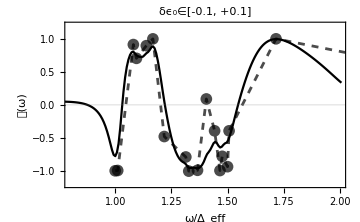
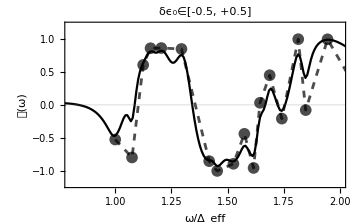

```mathematica
ϵ0=0.;SeedRandom[0608];
Row@*plotVisibility@@dataForPlot[ϵ0]
```

The figures above illustrate the frequency dependence of the visibility  in the presence of random onsite disorder. The left and right columns depict the topological and trivial regimes, respectively. The robustness against moderate onsite disorder demonstrates the potential of using visibility as a reliable measure for identifying Majorana zero modes.

## Paper Realizations

Figure 4 (a)(c)

Here we use the iconized saved data.

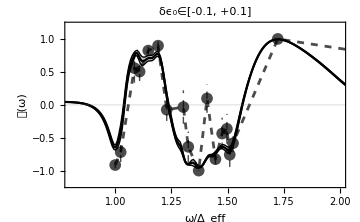
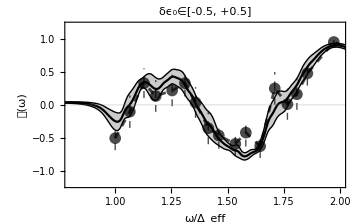

```mathematica
Row@plotVisibility[,,,]
```

Figure 4 (b)(d)

Here we use the iconized saved data.

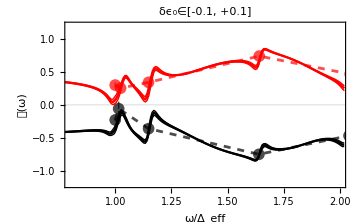
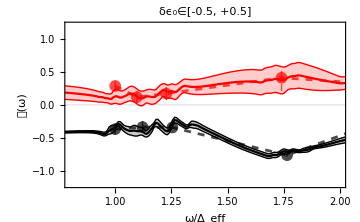

```mathematica
Row@MapThread[Show,plotVisibility@@@{{,,,,GrayLevel[0]},{,,,,RGBColor[1, 0, 0]}}]
```

Figure S3 (a)(c)

Here we use the iconized saved disorders.

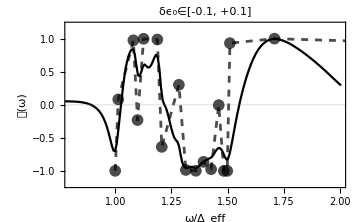
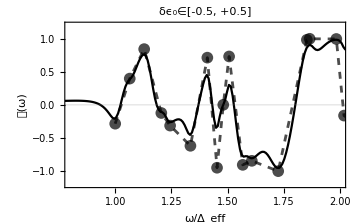

```mathematica
ϵ0=0.;
Row@*plotVisibility@@dataForPlot[ϵ0,]
```

Figure S3 (b)(d)

Here we use the iconized saved disorders and fine-tuned impurity.

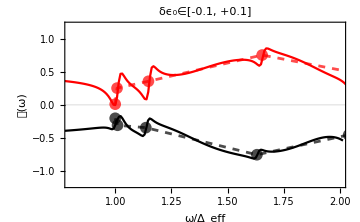
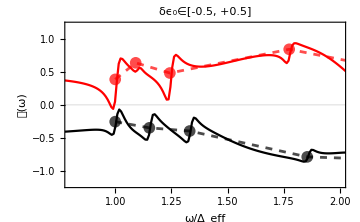

```mathematica
ϵ0=+0.13;ϵ0impurity=-0.0668511;
Row@MapThread[Show,plotVisibility@@@{Join[dataForPlot[ϵ0,,ϵ0impurity],{GrayLevel[0]}],Join[dataForPlot[ϵ0,,ϵ0impurity],{RGBColor[1, 0, 0]}]}]
```

Figure S4 (b)(d)

Here we use the iconized saved disorders and fine-tuned impurity.

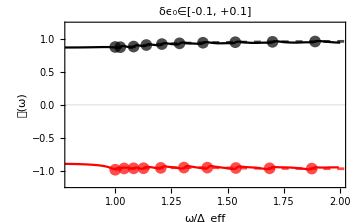
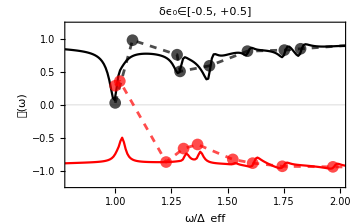

```mathematica
ϵ0=-0.2;ϵ0impurity=0.0334011;
Row@MapThread[Show,plotVisibility@@@{Join[dataForPlot[ϵ0,,ϵ0impurity],{GrayLevel[0]}],Join[dataForPlot[ϵ0,,ϵ0impurity],{RGBColor[1, 0, 0]}]}]
```

# Conclusion

In this notebook, we have studied the interaction between Majorana zero modes and magnons in ferromagnetically aligned magnetic impurities coupled to a spin-orbit-coupled s-wave superconductor. We uncovered the nonlocal Majorana zero modes’ imprints onto the uniform magnonic mode and demonstrated their intimate connection with the spatial symmetry of the chain. Furthermore, we discriminated the effects of Majorana zero mode and trivial zero modes from the magnonic response and showed the robustness of this response against moderate onsite disorder.
Our findings can be naturally extended to various other systems, such as two-dimensional magnetic clusters harboring chiral Majorana zero modes, superconducting-semiconducting nanowires covered by magnetic insulators, and carbon nanotubes proximitized by ferromagnets. The nonlocal Majorana-magnon coupling and the resultant parity-dependent spin susceptibility form the core of our study, presenting a novel method for detecting and characterizing Majorana zero modes.